## Calculate in the Infinite Stripe Geometry i.e., no hopping between the 1st and Nth sites (with the corrected Hamiltonian).

```mathematica
dimensionN=3
```

3

Now Construct the Hamiltonian Matrix

```mathematica
A=ⅈ*PauliMatrix[2]/2-PauliMatrix[3]/2;
A//MatrixForm
```

(-1/2 | 1/2
-1/2 | 1/2)

```mathematica
B[px_,m_]:=2Sin[px]*PauliMatrix[1]/2-2Cos[px]PauliMatrix[3]/2+(2-m)PauliMatrix[3];
B[px,m]//MatrixForm
```

(2-m-Cos[px] | Sin[px]
Sin[px] | -2+m+Cos[px])

```mathematica
CMatrix=-ⅈ*PauliMatrix[2]/2-PauliMatrix[3]/2;
CMatrix//MatrixForm
```

(-1/2 | -1/2
1/2 | 1/2)

```mathematica
For[i=1,i≤ dimensionN,i++,
If[i==1,
hamiltonianMLine[i][px_,m_]=ArrayFlatten[{{B[px,m],CMatrix,ConstantArray[0,{2,2*dimensionN-4}]}}]
];
If[i>1&&i<dimensionN,
hamiltonianMLine[i][px_,m_]=ArrayFlatten[{{
ConstantArray[0,{2,2*(i-2)}],A,B[px,m],CMatrix,ConstantArray[0,{2,2*dimensionN-2*(i+1)}]
}}]
];
If[i==dimensionN,
hamiltonianMLine[i][px_,m_]=ArrayFlatten[{{
ConstantArray[0,{2,2*(i-2)}],A,B[px,m]
}}]
];]
hamiltonianM[px_,m_]=hamiltonianMLine[1][px,m];
For[i=2,i≤dimensionN,i++,
hamiltonianM[px_,m_]=Join[hamiltonianM[px,m],hamiltonianMLine[i][px,m]];
]
```

```mathematica
hamiltonianM[px,m]//MatrixForm
```

(2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0
Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0
-1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2
-1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2
0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px]
0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px])

Solve the Eigenvalue Equation and Plot

```mathematica
eigenSystemResult[px_,m_]=Eigensystem[hamiltonianM[px,m]]
```

{{-1/2 √Root[-16032+33280 m-29824 m^2+14848 m^3-4416 m^4+768 m^5-64 m^6+22400 Cos[px]-44992 m Cos[px]+11+3072 m^3 Cos[2 px]-384 m^4 Cos[2 px]+896 Cos[3 px]-1472 m Cos[3 px]+768 m^2 Cos[3 px]-128 m^3 Cos[3 px]+(1776-2432 m+1376 m^2-384 m^3+48 m^4-2048 Cos[px]+2560 m Cos[px]-1152 m^2 Cos[px]+192 m^3 Cos[px]+368 Cos[2 px]-384 m Cos[2 px]+96 m^2 Cos[2 px]) #1+(-68+48 m-12 m^2+48 Cos[px]-24 m Cos[px]) #1^2+#1^3&,1],1/2 √Root[1],2,1,1/2 √Root[1&,3]},1}
 |  |  |  |

The eigensystem returns a 2 x (2*dimensionN) matrix, with the eigenvalues in the first line, and the corresponding eigenvectors in the second line.

```mathematica
Dimensions[eigenSystemResult[px,m]]
```

{2,6}

Now I seperate them and store them into respective arrays:

```mathematica
(* Experience tells me extrating things in eigenSystemResult outside is inefficient. Instead, define a new function of the component under investigation and plot using that function. Therefore, part of the following code are commented out. *)
eigenValues[px_,m_]=ConstantArray[0,{1,2*dimensionN}];
(* eigenVectors[px_,m_]=ConstantArray[0,{2*dimensionN,2*dimensionN}]; *)(* Labelled by ( ith eigenvector, jth component of that eigenvector ) *)
For[i=0,i≤(2 dimensionN),i++,
(*A primitive way that works: eigenValues[px_,m_][i]=eigenSystemResult[px,m][[1,i]];*)
eigenValues[px_,m_]=ReplacePart[eigenValues[px,m],{1,i}-> eigenSystemResult[px,m][[1,i]]];
(* For[j=0,j≤(2 dimensionN),j++,
eigenVectors[px_,m_]=ReplacePart[
eigenVectors[px,m],{i,j}-> eigenSystemResult[px,m][[2,i]][[j]]
];
]*)
]
```

```mathematica
Manipulate[
Plot[Evaluate[eigenValues[px,m]],{px,-π,π},PlotLegends->Automatic],
{m,-10,10}]
```

The crossing now happens at (m,px)= (1,0), (3,±π), And the band that crosses correspondes to the 1st and 2nd eigenvalues/eigenvectors

Now Analysis the Eigenvectors

```mathematica
f1[px_,m_]=eigenSystemResult[px,m][[2,1]][[1]];
f2[px_,m_]=eigenSystemResult[px,m][[2,1]][[2]];
f3[px_,m_]=eigenSystemResult[px,m][[2,1]][[3]];
f4[px_,m_]=eigenSystemResult[px,m][[2,1]][[4]];
f5[px_,m_]=eigenSystemResult[px,m][[2,1]][[5]];
f6[px_,m_]=eigenSystemResult[px,m][[2,1]][[6]];
g1[px_,m_]=eigenSystemResult[px,m][[2,2]][[1]];
```

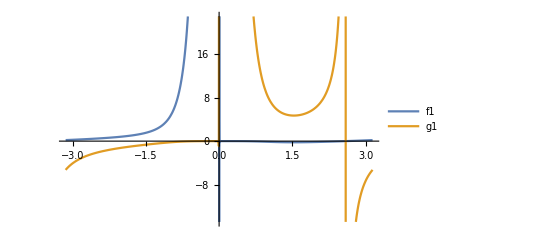

```mathematica
Plot[
{f1[px,1],g1[px,1]},{px,-π,π},PlotLegends->{"f1","g1"}]
```

```mathematica
Plot3D[f1[px,m],{px,-Pi,Pi},{m,0,4},MeshFunctions->{#2&},Mesh->10,PerformanceGoal->"Quality",MeshStyle->{{Black,Thin}}]
```

-Graphics3D-

```mathematica
Plot3D[g1[px,m],{px,-Pi,Pi},{m,0,4},MeshFunctions->{#2&},Mesh->10,PerformanceGoal->"Quality",MeshStyle->{{Black,Thin}}]
```

-Graphics3D-

```mathematica
Plot3D[f2[px,m],{px,-Pi,Pi},{m,0,4},MeshFunctions->{#2&},Mesh->10,PerformanceGoal->"Quality",MeshStyle->{{Black,Thin}}]
Plot3D[f3[px,m],{px,-Pi,Pi},{m,0,4},MeshFunctions->{#2&},Mesh->10,PerformanceGoal->"Quality",MeshStyle->{{Black,Thin}}]
Plot3D[f4[px,m],{px,-Pi,Pi},{m,0,4},MeshFunctions->{#2&},Mesh->10,PerformanceGoal->"Quality",MeshStyle->{{Black,Thin}}]
Plot3D[f5[px,m],{px,-Pi,Pi},{m,0,4},MeshFunctions->{#2&},Mesh->10,PerformanceGoal->"Quality",MeshStyle->{{Black,Thin}}]Plot3D[f6[px,m],{px,-Pi,Pi},{m,0,4},MeshFunctions->{#2&},Mesh->10,PerformanceGoal->"Quality",MeshStyle->{{Black,Thin}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

-Graphics3D- -Graphics3D-